# Lagrangian and Hamiltonian Dynamics of One Dimensional Systems.

Let’s explore the dynamics of the rotor system introduced in Section 7.2.1. Though the system is a two-dimensional system described by the coordinates θ(t), x(t), we will, as shown below, be able to reduce the dynamical equations into two one-dimensional second-order differential equations.

The Lagrangian of the translating rotor is given by Eq. 7.7
L=(M+m) (ẋ)^2/2 +  m L^2 (θ̇)^2/2-m θ̇ ẋ L sin(θ)
Since 
(∂ L)/(∂ẋ)=(M+m) ẋ -m θ̇  L sin(θ)     (∂ L)/(∂θ̇)=m L^2 θ̇ -m ẋ L sin(θ)     (∂ L)/(∂θ)= m θ̇ ẋ L cos(θ)
The Lagrange equations become
(M+m) ẍ +m (θ̇)^2 L cos(θ) -  θ̈ m L sin(θ)= 0
m L^2 θ̈-m ẍ L sin(θ) + m ẋ θ̇ L cos (θ)-  m θ̇ ẋ L cos(θ)=0
Or
  (M+m) ẍ +m (θ̇)^2 L cos(θ) -  θ̈ m L sin(θ)= 0
m L^2 θ̈-m ẍ L sin(θ)=0

Inserting the expression for ẍ from the first equation into the second we get

θ̈+m/(M+m  cos^2 θ) (θ̇)^2 cos(θ)sin(θ)=0

```mathematica
ClearAll["Global`*"]
```

We solve Eq. (1) for θ(t),

```mathematica
(* initializing parameters M,m,ω and L *)
M=1;m=1;ω=1;L=1;
solθ=Flatten[NDSolve[{θ''[t]+m/(M+m Cos[θ[t]]^2)( θ'[t])^2 Cos[θ[t]]Sin[θ[t]]==0,θ[0]==0,θ'[0]==ω},θ,{t,0,20Pi/ω}]];
θfun[t_]=θ[t] /. solθ
```

InterpolatingFunction[{{0., 62.8319}}, <>][t]

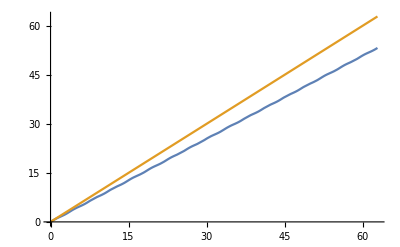

```mathematica
(* the solution is returned in θfun[t], which we plot below *)
Plot[{θfun[t],ω t},{t,0,20Pi/ω}]
```

In the figure, the blue line represents the solution for θ(t), whereas the beige line represents the relation θ(t) = ω t. Below we plot the angular velocity θ̇. It shows oscillations around a constant mean given by θ̇ = ω.

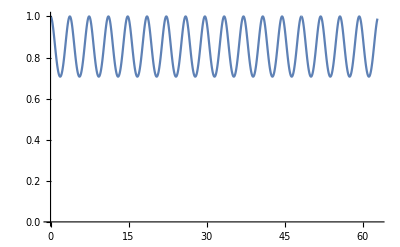

```mathematica
Plot[θfun'[t],{t,0,20Pi/ω},PlotRange->{0,1}]
```

We now solve for the x(t), representing the motion of the ion.

```mathematica
solx=Flatten[NDSolve[{x''[t]+m/(m+M) θfun'[t]^2 L Cos[θfun[t]]==0,x[0]==0,x'[0]==0},x,{t,0,20Pi/ω}]]
```

{x→InterpolatingFunction[{{0., 62.8319}}, <>]}

```mathematica
xfun[t_]=x[t] /. solx
```

InterpolatingFunction[{{0., 62.8319}}, <>][t]

We plot the solution xfun[t]

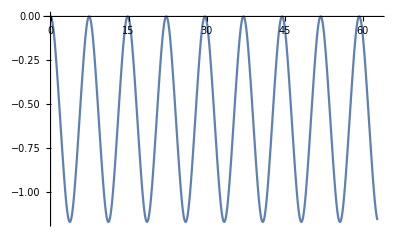

```mathematica
Plot[xfun[t],{t,0,20Pi/ω}]
```

This plot demonstrates that the ion oscillates around a mean position given by

```mathematica
xmean=NIntegrate[xfun[t],{t,0,20Pi/ω}]/(20 Pi/ω)
```

-0.582407

Using these results we can re-construct the motion of the electron and the ion. Below the electron is denoted by a red disk, whereas the the larger black disk represents the motion of the center of the ion.

```mathematica
g[t_]:=Graphics[Disk[{xfun[t],0},0.2]]
```

```mathematica
electron[t_]:={xfun[t]+ L Cos[θfun[t]],L Sin[θfun[t]]}
```

```mathematica
h[t_]:=Graphics[{Red,Disk[electron[t],0.1]}]
```

```mathematica
Manipulate[Show[h[t],g[t],PlotRange->{{-5.0,5.0},{-2,2}}],{t,0,20Pi/ω,0.01},SaveDefinitions->True]
```

### Exercise:

Explore the behavior of this dynamical system by adjusting the values of the ratio m/M.